```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
happyQ[num_Integer,base_Integer]:=Block[{x,seen},
seen={};
x= num;
Print[x];
While[
!MemberQ[seen,x]&&x>1,
x=Total[IntegerDigits[x,base]^2];
AppendTo[seen,x];
Print[x];
];
Print[x];
Return[x==1]
]
```

```mathematica
happyQ[12,2]
```

12

2

2

False

```mathematica
x=BaseForm[1,3]
```

1_3

```mathematica
x
```

```mathematica
x={};
```

```mathematica
AppendTo[x,1]
```

{1}

```mathematica
x
```

{1}

```mathematica
x==BaseForm[1,10]
```

1_3==1

```mathematica
Equal
```

## Generation

```mathematica
happies=Select[Range[1000000],happyQ]
```

{1,7,10,13,19,23,28,31,32,44,49,68,70,79,82,86,91,94,97,100,103,109,129,130,133,139,167,176,188,190,192,193,203,208,219,226,230,236,239,262,263,280,291,293,301,302,310,313,319,320,326,329,331,338,356,362,365,367,368,376,379,383,386,142945,999685,999686,999687,999694,999697,999701,999703,999708,999710,999713,999716,999730,999731,999733,999735,999738,999753,999761,999768,999769,999780,999783,999786,999796,999807,999823,999829,999832,999837,999839,999849,999856,999865,999866,999867,999870,999873,999876,999892,999893,999894,999899,999911,999912,999921,999928,999929,999938,999944,999945,999946,999948,999954,999964,999967,999976,999982,999983,999984,999989,999992,999998,1000000}
 |  |  |  |

```mathematica
DumpSave[NotebookDirectory[]<>"happy-numbers.mx",happies];
```

```mathematica
Get[NotebookDirectory[]<>"happy-numbers.mx"]
```

## SDL Complexity

```mathematica
Get[NotebookDirectory[]<>"sdl.mx"]
```

```mathematica
sdl[happies]
```

{0.839488,0.70032}

## Visibility analysis

```mathematica
<<visibility
```

plotModel

```mathematica
happyNumbers=happies[[;;10000]];
```

### Natural visibility

```mathematica
natLinks=naturalVisibilityLinks[happyNumbers]
```

{1→2,1→3,1→4,1→9,1→11,2→3,2→4,2→11,3→4,4→5,4→6,4→9,4→11,5→6,5→9,5→11,6→7,6→9,6→11,7→8,7→9,8→9,9→10,9→11,10→11,11→12,11→13,11→15,11→16,11→17,11→18,11→19,11→20,32239,9986→9989,9986→9990,9986→9992,9986→9993,9986→9995,9986→9996,9986→9998,9987→9988,9988→9989,9988→9990,9988→9998,9989→9990,9990→9991,9990→9992,9990→9993,9990→9996,9990→9998,9991→9992,9991→9993,9991→9998,9992→9993,9993→9994,9993→9995,9993→9996,9993→9998,9994→9995,9994→9996,9995→9996,9996→9997,9996→9998,9997→9998,9998→9999}
 |  |  |  |

```mathematica
DumpSave["natLinks.mx", natLinks];
```

```mathematica
Get["natLinks.mx"]
```

```mathematica
natGraph=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|5→1422,4→1867,3→1885,7→608,8→435,18→50,2→977,11→182,9→302,6→866,14→163,17→61,22→26,43→2,10→269,12→172,16→91,20→43,13→156,26→20,23→31,35→10,30→9,24→29,55→3,41→3,89→1,21→32,15→100,19→46,25→21,37→6,32→14,27→13,29→12,48→5,45→1,34→10,66→1,44→5,74→1,36→4,73→1,76→1,28→7,31→9,33→5,42→2,46→2,39→3,47→1,53→1,49→2,83→2,38→4,50→1,51→1,59→1,40→1,1→1|>

```mathematica
count[1]=.
```

```mathematica
count[2]=.
```

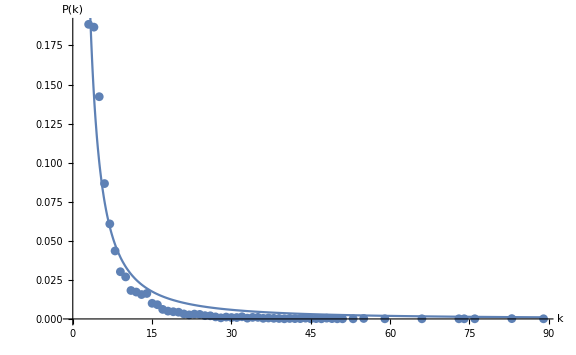
{{C→1.29634,γ→1.58904},-Graphics-}

```mathematica
plotModel[count,10000]
```

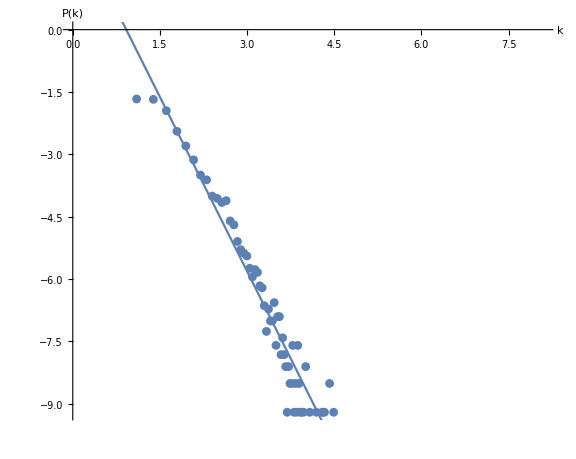

```mathematica
plotLinearModel[count,10000]
```

```mathematica
Export["happy-natural.pdf",%60]
```

happy-natural.pdf

### Horizontal visibility

```mathematica
horLinks=horizontalVisibilityLinks[happyNumbers]
```

{1→2,1→4,2→3,3→4,4→5,4→6,4→9,5→6,6→7,6→9,7→8,7→9,8→9,9→10,9→11,10→11,11→12,11→13,11→22,12→13,13→14,13→15,13→16,13→21,13→22,14→15,15→16,16→17,16→21,17→18,18→19,19→20,18559,9980→9981,9981→9982,9982→9983,9982→9985,9983→9984,9984→9985,9985→9986,9986→9987,9986→9988,9986→9990,9986→9996,9986→9998,9987→9988,9988→9989,9988→9990,9989→9990,9990→9991,9990→9993,9990→9996,9991→9992,9991→9993,9992→9993,9993→9994,9993→9995,9993→9996,9994→9995,9995→9996,9996→9997,9996→9998,9997→9998,9998→9999}
 |  |  |  |

```mathematica
DumpSave["horLinks.mx", horLinks];
```

```mathematica
horGraph=Graph[horLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[horGraph]//Counts
```

<|2→3767,5→806,4→1409,6→570,3→2328,7→432,10→87,9→155,8→269,12→44,11→69,15→6,13→24,21→1,18→3,14→15,19→1,17→6,16→5,23→1,1→1|>

```mathematica
count[1]=.
```

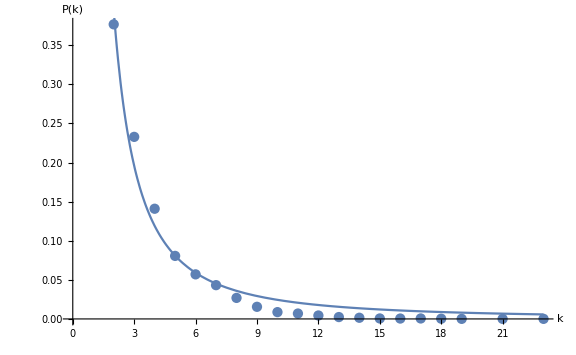
{{C→1.30865,γ→1.72953},-Graphics-}

```mathematica
plotModel[count, 10000]
```

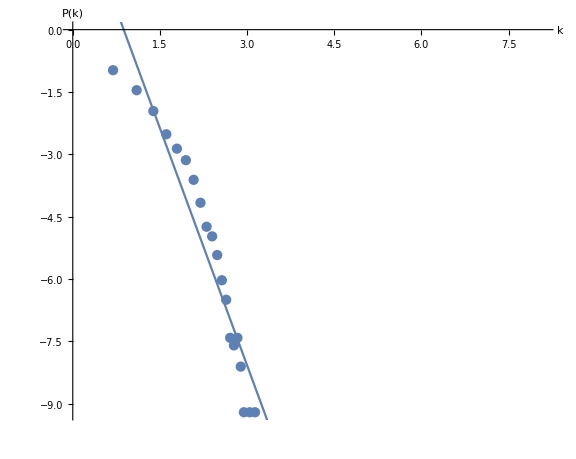

```mathematica
plotLinearModel[count, 10000]
```

```mathematica
Export["happy-horizontal.pdf",%67]
```

happy-horizontal.pdf